# Andre Lukas MM PS 1 - Q1

Defining the weight function and the scalar product.

```mathematica
weight[x_] := Exp[-x^2]
scalarProduct[f_, g_] := Integrate[(f * g * weight[x]), {x, -Infinity, Infinity}]
```

Defining Gram-Schmidt procedure. Takes input list of functions and forms them into an orthonormal basis relative to the above.

```mathematica
basis = {};
n = 7; (*Maximal order of basis*)
fs= Table[x^i, {i, 0, n}];  (*List of functions to turn into orthonormal basis*)

(*Gram-Schmidt process for remaining basis vectors*)
For[i = 1, i <= Length[fs], i++, (*Iterating over each function*)
For[j = 1, j <= Length[basis], j++,
fs[[i]] = fs[[i]] - scalarProduct[fs[[i]], basis[[j]]]*basis[[j]]];(*Subtracting relevant projections from each function*)
AppendTo[basis, fs[[i]] / Sqrt[scalarProduct[fs[[i]], fs[[i]]]]];
]

basis
```

{1/π^(1/4),(√2 x)/π^(1/4),(√2 (-1/2+x^2))/π^(1/4),(2 (-(3 x)/2+x^3))/(√3 π^(1/4)),(√(2/3) (-3/4+x^4-3 (-1/2+x^2)))/π^(1/4),(2 (-(15 x)/4+x^5-5 (-(3 x)/2+x^3)))/(√15 π^(1/4)),(2 (-15/8+x^6-45/4 (-1/2+x^2)-15/2 (-3/4+x^4-3 (-1/2+x^2))))/(3 √5 π^(1/4)),(2 √(2/35) (-(105 x)/8+x^7-105/4 (-(3 x)/2+x^3)-21/2 (-(15 x)/4+x^5-5 (-(3 x)/2+x^3))))/(3 π^(1/4))}

Can now consider the projection of some more general function onto this basis, and using the result as an approximation.

```mathematica
f[x_] = Sin[x];(*Defining a general function*)
approxF = {}; (*ith element refers to f approximated with i basis polynomials, that being to (i-1)th order*)
current = 0;

For[i = 1, i <= Length[basis], i++,
current += scalarProduct[f[x], basis[[i]]]*basis[[i]];
AppendTo[approxF, current]]
```

To plot all of the approximations together.

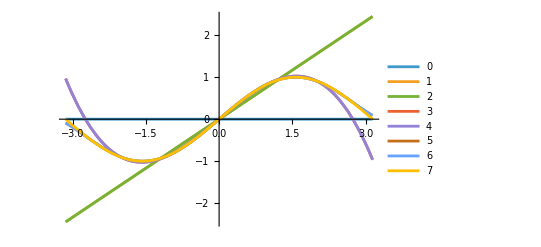

```mathematica
labels = Table[ToString[i], {i, 0, n}];
Plot[approxF, {x, -Pi, Pi}, PlotLegends->labels]
```

To plot the highest order approximation against the given function.

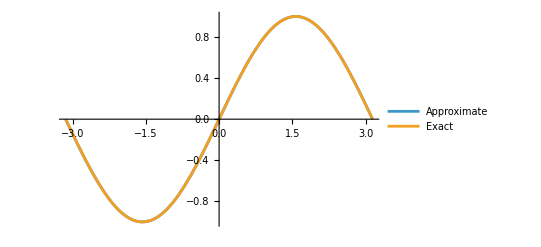

```mathematica
Plot[{approxF[[-1]], f[x]}, {x, -Pi, Pi}, PlotLegends->{"Approximate", "Exact"}]
```